```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];
memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};
Dimensions[data1]
data1=Transpose[data1];
For[i=1,i≤ Dimensions[data1][[1]],i++,{
For[j=1,j≤ Dimensions[data1][[2]],j++,{
data1[[i,j]]-=2;
If[i<2,data1[[i,j]]=0];
}]
}]
ArrayPlot[data1,PlotRange->All,ColorFunction->"Rainbow",Mesh->showmesh,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True]
```

IR549

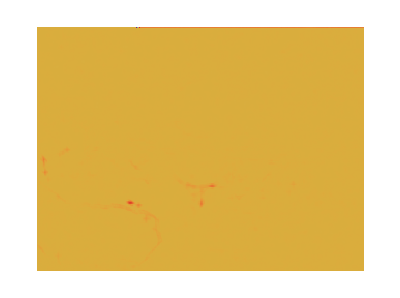
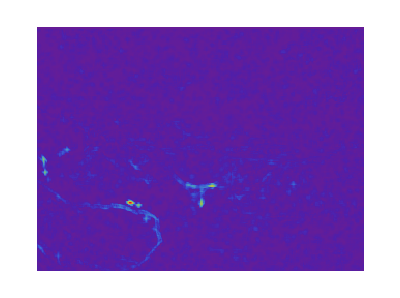
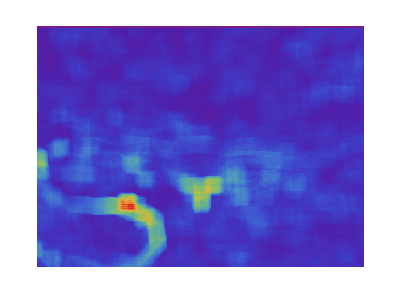
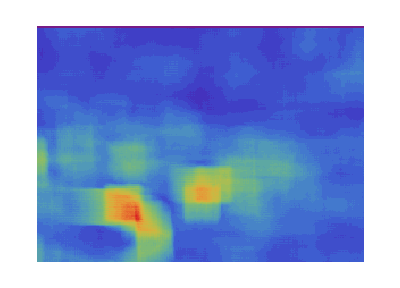
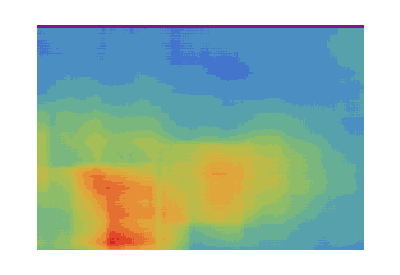
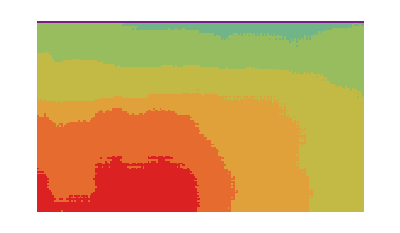
```mathematica
{{IR549, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR550

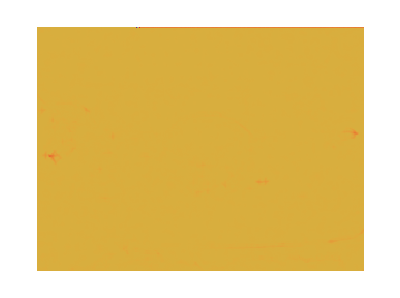
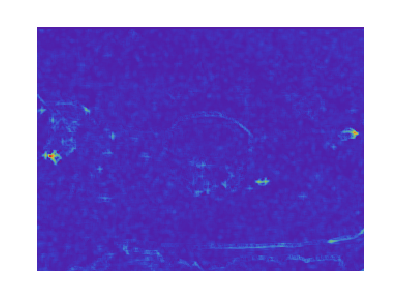
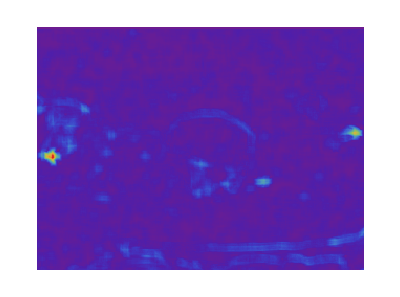
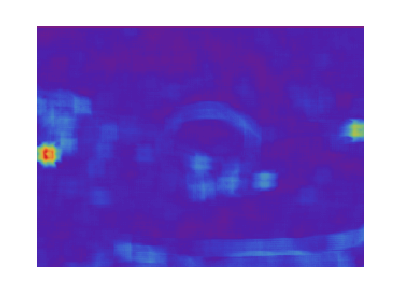
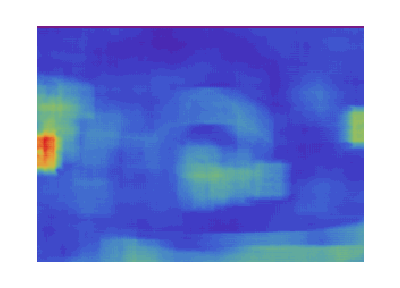
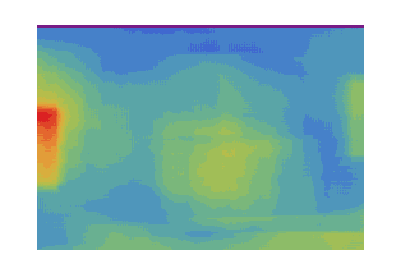
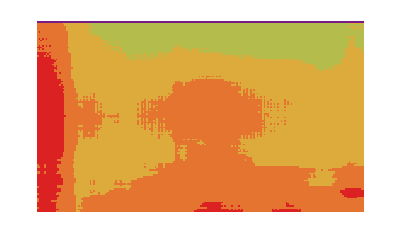
```mathematica
{{IR550, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR553

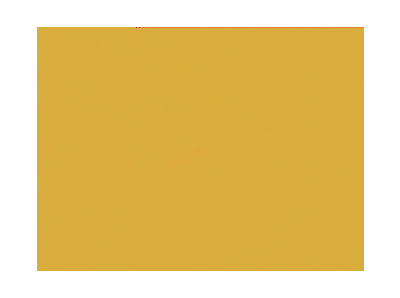
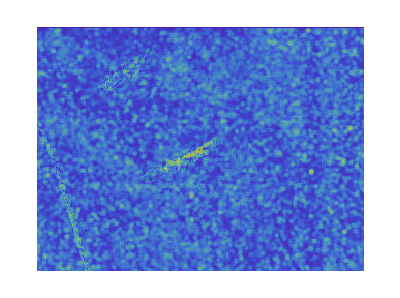
```mathematica
{{IR553, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR558

```mathematica
{{IR558, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR573

```mathematica
{{IR573, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR576

```mathematica
{{IR576, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR587

```mathematica
{{IR587, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```

IR590

```mathematica
{{IR590, -Graphics-}, {s3_0
All Δ, -Graphics-}, {s3
Subscript[Δ, i<3]=0, -Graphics-}, {s4
Subscript[Δ, i<3]=0, -Graphics-}, {s5
Subscript[Δ, i<3]=0, -Graphics-}, {s6
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<3]=0, -Graphics-}, {s7
Subscript[Δ, i<2]=0, -Graphics-}, {LEGEND, color ranges:: Δ=(Subscript[D, F]-2)10; [[10*Normal Dimension]]}}
```